```mathematica
ode=y'[x]+y[x]/5-ⅇ^(-x/5)Cos[x]==0
```

-ⅇ^(-x/5) Cos[x]+y[x]/5+y'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→ⅇ^(-x/5) (C[1]+Sin[x])}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==0},y[x],x]]
```

{{y[x]→ⅇ^(-x/5) Sin[x]}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])

```mathematica
dyadx[x_]:=1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])
```

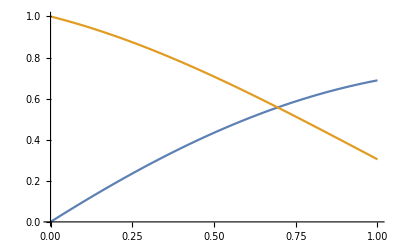

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```

```mathematica
Limit[y/(√(1-y^2)),y->1]
```

(-ⅈ) ∞